#### 0. define parameters and functions

```mathematica
Clear[xa, xb, ea, kT, lmd]
xa=3/2;xb=2;
ea=10;
kT=4012/1000;
$MaxExtraPrecision = 200;
lmd[i_, f_, eb_, ea_]:=1000i*(Exp[-ea+f*xa/(i*kT)]+Exp[-eb+f*xb/(i*kT)])
```

#### 1. PDF

```mathematica
Clear[pdf, pdf0, ea]
(*Distribution of cluster lifetime under shared force, without rebinding*)
pdf[t_, n_, f_, eb_, ea_]:=Module[{},
Clear[pt, tmp, ix, jx];
pt=0;
For[ix=1,ix<n+1, ix++, {
tmp=1;
For[jx=1,jx<n+1, jx++,{
If[jx≠ix, 
tmp = tmp*lmd[jx, f, eb, ea]/(lmd[jx, f, eb, ea]-lmd[ix, f, eb, ea])
];}
];
pt = pt+tmp*lmd[ix, f, eb, ea]*Exp[-lmd[ix, f, eb, ea]*t];
}];
Clear[tmp, ix, jx];
pt
]

(*Distribution of cluster lifetime no force, without rebinding*)
pdf0[t_, n_, eb_]:=Module[{}, 
Clear[lmd0];
lmd0=lmd[1, 0, eb];
n*lmd0*Exp[-lmd0*t]*(1-Exp[-lmd0*t])^(n-1)
]
(*Print["pdf=", N[pdf[2, 20, 0, 0], 5], ", pdf0=",N[pdf0[2, 20, 0], 5]]*)
```

```mathematica
tlist = Table[6*ti/200, {ti, 0, 200}];
pdflist0= Table[{tlist[[i]]/TmeanF[20, 1, 1, 0], N[pdf[tlist[[i]],20,0, 0], 6]*TmeanF[20, 1, 1, 0]}, {i, 1, Length[tlist]}];
```

```mathematica
tlist = Table[5*ti/200, {ti, 0, 200}];
pdflist1 = Table[{tlist[[i]]/TmeanF[20, 1, 1, 2], N[pdf[tlist[[i]],20,2, 0]*TmeanF[20, 1, 1, 2], 6]}, {i, 1, Length[tlist]}];
```

```mathematica
tlist = Table[1*ti/200, {ti, 0, 200}];
pdflist2 = Table[{tlist[[i]]/TmeanF[20, 1, 1, 20], N[pdf[tlist[[i]],20,20, 0], 6]*TmeanF[20, 1, 1, 20]}, {i, 1, Length[tlist]}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 200. reached while evaluating (2432902008176640000 (ⅇ^(375/1003)+ⅇ^(500/1003)) «17» (ⅇ^(3750/1003)+ⅇ^(5000/1003)) (ⅇ^(7500/1003)+ⅇ^(10000/1003)))/((20 (ⅇ^(375/1003)+ⅇ^(500/1003))-2 (ⅇ^(3750/1003)+ⅇ^(5000/1003))) «17» (3 (ⅇ^(2500/1003)+ⅇ^(10000/3009))-2 (ⅇ^(3750/1003)+ⅇ^(5000/1003))))+(«1»)/((«1») «17» («1»))+(«1»)/(«1»)+«15»+(«1»)/(«1»)+(2432902008176640000 «19» (ⅇ^(«1»)+«1»))/(«1»).

```mathematica
tlist = Table[0.00002*ti/200, {ti, 0, 200}];
pdflist3 = Table[{tlist[[i]]/TmeanF[20, 1, 1, 400], N[pdf[tlist[[i]],20,400, 0], 6]*TmeanF[20, 1, 1, 400]}, {i, 1, Length[tlist]}];
```

General::munfl: Exp[-3.97282×10^79] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.98639×10^36] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.2054×10^22] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
pdflist1= Table[{tlist[[i]], N[pdf[tlist[[i]], 1,20, 0], 6]}, {i, 1, Length[tlist]}];
```

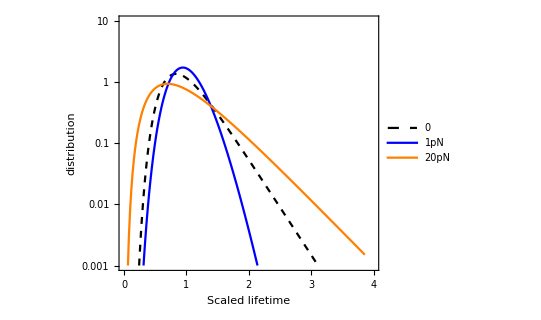

```mathematica
Show[
(*LogPlot[{ pdf0[tx, 20, 0]/TmeanF[20, 1, 1, 0]}, {tx, 0,5}, PlotRange->{0.001, 100},(*PlotRange->{-0.1, 8},*) PlotStyle->Red],*)
ListLogPlot[{pdflist0,  pdflist2, pdflist3}, Joined->True, PlotStyle->{{Black, Dashed}, {Blue},{Orange}},PlotRange->{{0, 4},{0.001, 10}},PlotRange->All, PlotMarkers->None,PlotLegends->Placed[{"0",  "1pN", "20pN"},{0.3, 0.25}]],Frame->True, FrameLabel->{"Scaled lifetime", "distribution"},FrameStyle->Directive[16], AspectRatio->0.8
]
```

General::munfl: 9.81803×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.01336×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.24864×10^-315 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

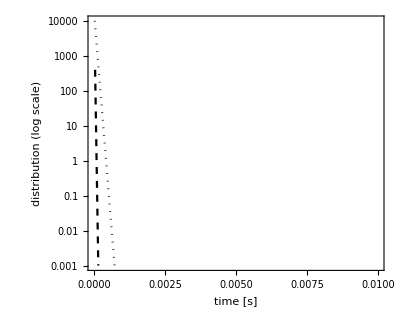

```mathematica
Show[
(*LogPlot[{pdf0[tx, 1, 0],pdf0[tx, 5, 0], pdf0[tx, 20, 0], pdf0[tx, 50, 0]}, {tx, 0, 8}, PlotRange->{0.0001, 1}, PlotStyle->{{Black,  Dotted},{Black, Dashed},{Black, Dashing[{0.03, 0.1-0.07}]},{Black, Thick}}],*)
ListLogPlot[{pdflist1, pdflist5,pdflist2,  pdflist}, Joined->True, PlotRange->{0.001, 10000},PlotStyle->{{Black,  Dotted},{Black, Dashed},{Black, Dashing[{0.03, 0.1-0.07}]},{Black, Thick}}
(*PlotLegends->Placed[{"N=1", "N=5", "N=20", "N=50"}, {0.8, 0.8}]*)],
Frame->True,AspectRatio->0.8,
FrameLabel->{"time [s]", "distribution (log scale)"},

FrameStyle->Directive[20]]
```

```mathematica
tlist = Table[1*ti/200, {ti, 0, 200}];
pdflist1 = Table[{tlist[[i]], N[pdf[tlist[[i]],30,30, 0], 6]}, {i, 1, Length[tlist]}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 200. reached while evaluating (265252859812191058636308480000000 (ⅇ^(375/1003)+ⅇ^(500/1003)) (ⅇ^(11250/29087)+ⅇ^(15000/29087)) «27» (ⅇ^(11250/1003)+ⅇ^(15000/1003)) «10»)/((30 (ⅇ^(375/1003)+ⅇ^(500/1003))-2 (ⅇ^(5625/1003)+ⅇ^(7500/1003))) «17» (13 (ⅇ^(11250/13039)+ⅇ^(15000/13039))-2 (ⅇ^(5625/1003)+ⅇ^(7500/1003))))+(«1»)/(«1»)+(«1»)/(«1»)+(«1»)/(«1»)+«23»+(«1»)/(«1»)+(«1»)/(«1»)+(«1»)/(«1»).

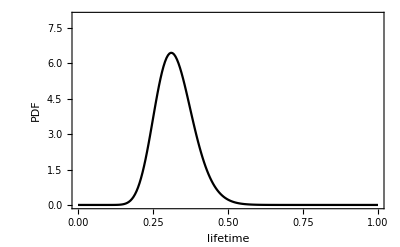

```mathematica
Show[ ListPlot[{pdflist1}, Joined->True, PlotStyle->Black, PlotRange->{{0, 1},{0, 8}},PlotRange->All, PlotMarkers->None],Frame->True, FrameLabel->{"lifetime", "PDF"},FrameStyle->Directive[18]
]
```

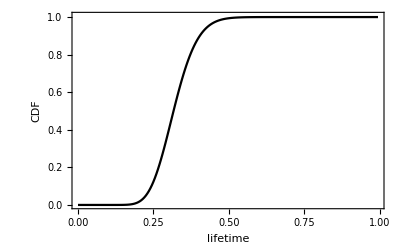

```mathematica
Show[ ListPlot[Table[{pdflist1[[ti, 1]], Sum[pdflist1[[tj, 2]]/200,{tj, 1, ti}]}, {ti, 1, 200}], Joined->True, PlotStyle->Black,PlotRange->{0, 1.005}, PlotMarkers->None],Frame->True, FrameLabel->{"lifetime", "CDF"},FrameStyle->Directive[18]
]
```

```mathematica
normal[x_, mu_, sigma_]:=1/(Sqrt[2 Pi]sigma) Exp[-(x-mu)^2/(2sigma^2)]
```

```mathematica
Show[ListLogPlot[{pdflist2,  pdflist}, Joined->True, PlotRange->{0.001, 10},PlotStyle->{{Black,  Dotted},{Black, Thick}},
PlotLegends->Placed[{ "N=20", "N=50"}, {0.8, 0.8}]],
LogPlot[{
normal[xx, tmean[20, 20, 0], Sqrt[tvar[20, 20, 0]]],
normal[xx, tmean[50, 50, 0], Sqrt[tvar[50, 50, 0]]]
}, {xx, 0, 1}, PlotStyle->{{Dotted, Red}, {Thick, Red}}],
Frame->True,AspectRatio->0.8,
FrameLabel->{"time [s]", "distribution (log scale)"},
FrameStyle->Directive[20]]
```

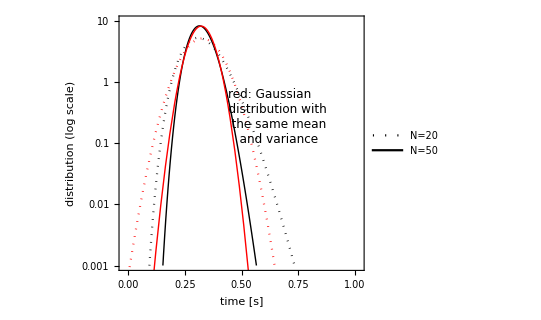

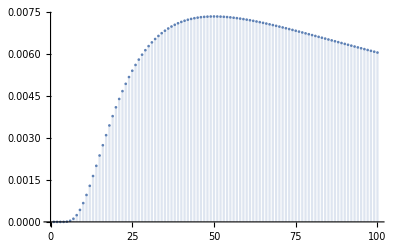

```mathematica
DiscretePlot[1/(mi Exp[50/mi]), {mi, 0, 100}]
```

#### 2. First two moments

```mathematica
tmean[n_, f_, eb_]:=Sum[1/lmd[i, f, eb], {i, 1, n}]
tvar[n_, f_, eb_]:=Sum[1/lmd[i, f, eb]^2, {i, 1, n}]
tsens[n_, f_, eb_]:=Sum[-i*Exp[-eb + f xb/(i*kT)]/lmd[i, f, eb]^2, {i, 1, n}]
tvarsens[n_, f_, eb_]:=Sum[-2*i*Exp[-eb + f xb/(i*kT)]/lmd[i, f, eb]^3, {i, 1, n}]
```

```mathematica
Print["expected: tmean=",N[ tmean[20, 20, 0],5], ", tvar=", N[tvar[20, 20, 0],5]]
Print["calulcated: tmean = ", Sum[tlist[[i]]*pdflist[[i]][[2]]/200, {i, 1, Length[tlist]}],
",tvar= ", Sum[(tlist[[i]]-tmean[20, 20, 0])^2*pdflist[[i]][[2]]/200, {i, 1, Length[tlist]}]]
```

expected: tmean=0.32619, tvar=0.0059854

calulcated: tmean = 0.326194,tvar= 0.00598537

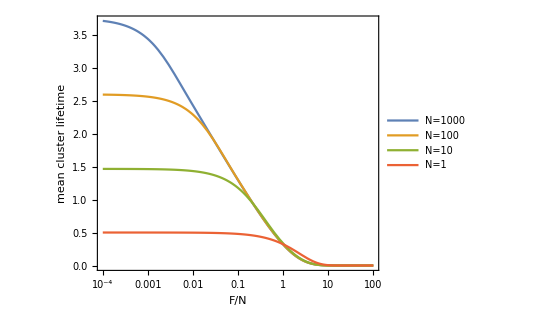

```mathematica
LogLinearPlot[{
tmean[1000, fx*1000, 0],tmean[100, fx*100, 0],tmean[10, fx*10, 0],tmean[1, fx, 0]
},{fx, 0.0001, 100},Frame->True,AspectRatio->0.8,
PlotLegends->Placed[{"N=1000", "N=100", "N=10", "N=1"}, {0.8, 0.7}],
FrameLabel->{"F/N", "mean cluster lifetime"},

FrameStyle->Directive[20]]
```

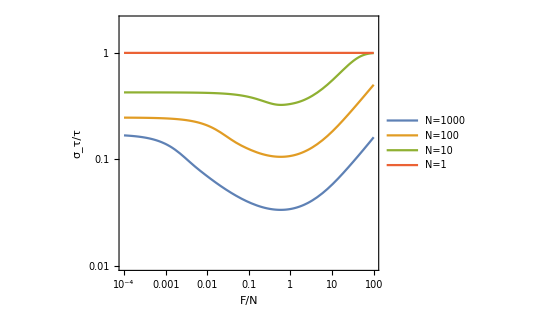

```mathematica
LogLogPlot[{
Sqrt[tvar[1000, fx*1000, 0]]/tmean[1000, fx*1000, 0],Sqrt[tvar[100, fx*100, 0]]/tmean[100, fx*100, 0],Sqrt[tvar[10, fx*10, 0]]/tmean[10, fx*10, 0],Sqrt[tvar[1, fx*1, 0]]/tmean[1, fx, 0]
},{fx, 0.0001, 100},Frame->True,AspectRatio->0.8, PlotRange->{0.01, 2},
PlotLegends->Placed[{"N=1000", "N=100", "N=10", "N=1"}, {0.17, 0.2}],
FrameLabel->{"F/N", "σ_τ/τ"},FrameStyle->Directive[20]]
```

General::munfl: 1/((1.77367×10^108)^3) is too small to represent as a normalized machine number; precision may be lost.

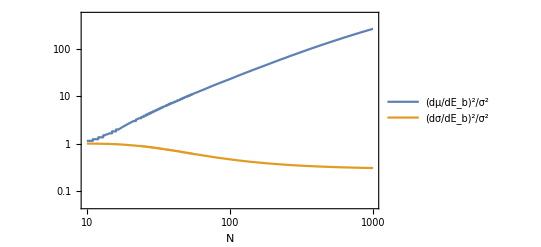

```mathematica
LogLogPlot[{(tsens[nx, 500, 0])^2/tvar[nx, 500, 0], (tvarsens[nx, 500, 0]/tvar[nx, 500, 0])^2/4}, {nx, 10, 1000}, PlotRange->{0.05, 500},
PlotLegends->Placed[{"(dμ/dE_b)^2/σ^2", "(dσ/dE_b)^2/σ^2"}, {0.2, 0.8}],
Frame->True,
FrameLabel->{"N", ""}]
```

#### 3. Derivative of PDF with respect to Eb

```mathematica
Clear[dpdf, dpdf0]
dpdf[t_, n_, f_, eb_]:=Module[
{},
Clear[dpt, tmp, ix, jx, part1, part2, part3, prods];
prods = Table[Product[lmd[jx, f, eb]/(lmd[jx, f, eb]-lmd[ix, f, eb]), {jx, 1, ix-1}]*Product[lmd[jx, f, eb]/(lmd[jx, f, eb]-lmd[ix, f, eb]), {jx, ix+1, n}], {ix, 1, n}];

dpt=0;

For[ix=1,ix<n+1, ix++, {
tmp=1;
part1 = Exp[-lmd[ix, f, eb]*t]*(1-lmd[ix, f, eb]*t)*prods[[ix]];
part2=0;part3=0;
For[jx=1,jx<n+1, jx++,{
If[jx≠ix, 
part2 = part2 + prods[[ix]]lmd[ix, f, eb] Exp[-lmd[ix, f, eb]t]/(lmd[jx, f, eb]-lmd[ix, f, eb]);
part3 = part3+ prods[[jx]] * (lmd[jx, f, eb]^2 )*Exp[-lmd[jx, f, eb]t]/(lmd[ix, f, eb]*(lmd[ix, f, eb]-lmd[jx, f, eb]))
];}
];
dpt =  dpt -ix* Exp[-eb +f xb/(ix*kT)]*(part1 +part2 - part3)
}];
Clear[ tmp, ix, jx, part1, part2, part3, prods];
dpt
]

dpdf0[t_, n_, f_, eb_]:=Module[{}, 
Clear[lmd0];
lmd0=lmd[1, 0, eb];
-n*Exp[-eb]Exp[-lmd0*t]*(1-Exp[-lmd0*t])^(n-2)((1-lmd0*t)(1-Exp[-lmd0 t])+(n-1)lmd0 t Exp[-lmd0 t])
]

Print["dpdf[t, n, f, eb]=",N[ dpdf[1, 50, 0, 1], 5]]
Print["expect: dpdf0=", N[dpdf0[1, 50, 0, 1], 6]]
Print["numerical delta pdf=", (N[pdf[1, 50, 0, 1+1/20], 6]-N[pdf[1, 50, 0, 1-1/20], 6])/(1/10)]
```

dpdf[t, n, f, eb]=-0.00005877

expect: dpdf0=-0.0000587698

numerical delta pdf=-0.000059888

```mathematica
Print["dpdf[t, n, f, eb]=",N[ dpdf[5, 20, 10, 1], 5]]
Print["numerical delta pdf=", (N[pdf[5, 20, 10, 1+1/20], 6]-N[pdf[5, 20, 10, 1-1/20], 6])/(1/10)]
```

dpdf[t, n, f, eb]=1.4908×10^-20

numerical delta pdf=1.7928×10^-20

#### 4. Fisher information

```mathematica
fisherinfo[n_, f_, eb_]:=Module[{},
Clear[tm, info, iz, tz];
tm =10*tmean[n, f, eb];ngrid=200;
dtx=tm/ngrid;
If[False,
Print["tm=", tm];
];
info = 0;
For[iz=1, iz≤ngrid, iz++, 
{
tz =tm*iz/ngrid;
info +=dtx* N[ dpdf[tz, n, f, eb]^2/pdf[tz, n, f, eb], 6]
}];
Clear[tm, iz,  dtx, ngrid, tz];
N[info, 10]
]


fisherinfo0[n_,  eb_]:=Exp[-2 eb]/(lmd[1,0, eb ]^2)*(1+NIntegrate[n(n-1)t^2 Exp[-2 t](1-Exp[-t])^(n-3), {t, 0, Infinity}])

fisherinfoGaussian[n_, f_, eb_, alpha_:0]:=((tsens[n ,f, eb])^2+alpha*2*tvarsens[n, f, eb]^2/tvar[n, f, eb])/tvar[n, f, eb]

(*Print["fisher info=", fisherinfo[20, 0, 0]]*)
Print["expected=", N[fisherinfo0[20, 0]]]
Print["Gaussian approx=", N[fisherinfoGaussian[20, 0, 0]]]
```

expected=2.21796

Gaussian approx=2.02732

```mathematica
Print["fisher info=", fisherinfo[10, 500, -2]]
Print["Gaussian approx=", N[fisherinfoGaussian[10,500, -2,0]]]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

fisher info=1.15066

General::munfl: 1/((1.31058×10^109)^3) is too small to represent as a normalized machine number; precision may be lost.

Gaussian approx=1.14339

```mathematica
Print["fisher info=", fisherinfo[5, 500, 0]*1000/5]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

fisher info=194.226

```mathematica
Table[{i, fisherinfo[i, 500, 0]*1000/i}, {i, 1,10}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{1,971.131},{2,485.565},{3,323.71},{4,242.783},{5,194.226},{6,161.894},{7,139.13},{8,123.941},{9,117.347},{10,114.707}}

```mathematica
Table[{i, fisherinfo[i, 500, 10]*1000/i}, {i, 1,10}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{1,971.131},{2,485.565},{3,323.697},{4,240.958},{5,164.923},{6,57.3669},{7,8.7618},{8,1.44739},{9,0.329087},{10,0.0972162}}

```mathematica
Table[{i, fisherinfo[i, 500, 5]*1000/i}, {i, 1,10}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{1,971.131},{2,485.565},{3,323.71},{4,242.77},{5,194.004},{6,160.43},{7,133.717},{8,110.308},{9,90.7741},{10,72.0349}}

```mathematica
Table[{i, fisherinfo[i, 500, -2]*1000/i}, {i, 1,11}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{1,971.131},{2,485.565},{3,323.71},{4,242.783},{5,194.227},{6,161.902},{7,139.163},{8,124.028},{9,117.537},{10,115.066},{11,115.268}}

```mathematica
sss = Table[{i, fisherinfo[i, 500, -2]*1000/i}, {i, 12,15, 2}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

{{12,117.378},{14,124.327}}

```mathematica
fisherinfo[50, 500, -2]*1000/50
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

281.041

```mathematica
Table[{i, fisherinfo[i, 500, 2]*1000/i}, {i, 1,10}]
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

```mathematica
N[{{1,971.1308332594784878552`6.},{2,485.5654166295280131551`6.},{3,323.7102731924127655353`6.},{4,242.7820930520067609895`6.},{5,194.2160142447845749564`6.},{6,161.829786082677099749`6.},{7,138.888868564242927902`6.},{8,123.2980597934687141129`6.},{9,115.9580380571138418601`6.},{10,112.1068123906574338694`6.}}, 5]
```

{{1.,971.13},{2.,485.57},{3.,323.71},{4.,242.78},{5.,194.22},{6.,161.83},{7.,138.89},{8.,123.3},{9.,115.96},{10.,112.11}}

```mathematica
n0=5;
eblist=Table[-5+10*i/10, {i, 0, 10}];
infolist = Table[{eblist[[i]], fisherinfo[n0, n0, eblist[[i]]]}, {i, 1, Length[eblist]}];
```

```mathematica
infolist0 = Table[{eblist[[i]], fisherinfo[n0, 0, eblist[[i]]]}, {i, 1, Length[eblist]}];
```

```mathematica
infolist5= Table[{eblist[[i]], fisherinfo[n0,5 n0, eblist[[i]]]}, {i, 1, Length[eblist]}];
```

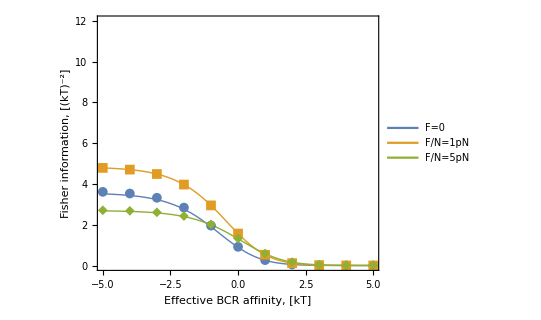

```mathematica
Show[

Plot[{
fisherinfoGaussian[n0, 0, ebx],
fisherinfoGaussian[n0, 1n0, ebx],
fisherinfoGaussian[n0, 5n0, ebx]
}, {ebx, -5, 5}, PlotStyle->Thick, PlotRange->{0, 12},
PlotLegends->Placed[{"F=0", "F/N=1pN", "F/N=5pN"},{0.7, 0.7}]],
(*Plot[fisherinfo0[10, ebx], {ebx, -5, 10},PlotRange->{0, 12}],*)
ListPlot[{infolist0, infolist, infolist5}, PlotMarkers->{Automatic,  Medium}(*PlotStyle->ColorData[97, "ColorList"][[2]]*)],
Frame->True,PlotStyle->Dashed,
(*PlotRange->{0.001, 10},*)
FrameLabel->{"Effective BCR affinity, [kT]", "Fisher information, [(kT)^-2]"},
FrameStyle->Directive[15],
AspectRatio->0.8
]
```

```mathematica
nlistT =Table[i, {i, 1, 15}];
(*infolistT = Table[{nlistT[[i]], fisherinfo[nlistT[[i]],5nlistT[[i]],- Log[0.1]]}, {i, 1, Length[nlistT]}];*)
```

```mathematica
infolistT1= Table[{nlistT[[i]], fisherinfo[nlistT[[i]],nlistT[[i]],0]}, {i, 1, Length[nlistT]}];
```

```mathematica
infolistT0= Table[{nlistT[[i]], fisherinfo[nlistT[[i]],0,0]}, {i, 1, Length[nlistT]}];
```

```mathematica
infolistT40= Table[{nlistT[[i]], fisherinfo[nlistT[[i]],40nlistT[[i]],0]}, {i, 1, Length[nlistT]}];
```

General::unfl: Underflow occurred in computation.

General::stop: Further output of General::unfl will be suppressed during this calculation.

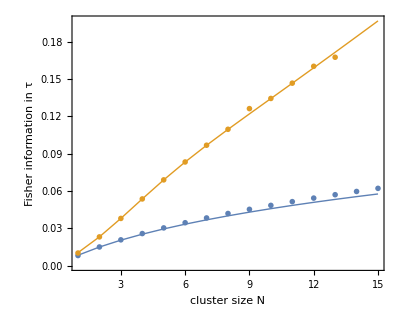

```mathematica
Show[
DiscretePlot[
{fisherinfoGaussian[ni,0ni,  -Log[0.1], 0],
fisherinfoGaussian[ni,ni,  -Log[0.1], 0]
}, {ni, 1, 15}, Joined->True, Filling->False, PlotStyle->Thick],
ListPlot[{infolistT0, infolistT1}, PlotMarkers->{{●,Large}, {●,Large}}],
Frame->True,AspectRatio->0.8,
FrameLabel->{"cluster size N", "Fisher information in τ"},
FrameStyle->Directive[16]]
```

```mathematica
ListPlot[{testData1,testData2,testData3},PlotMarkers->{{●,10},{▲,10},{■,10}}]
```

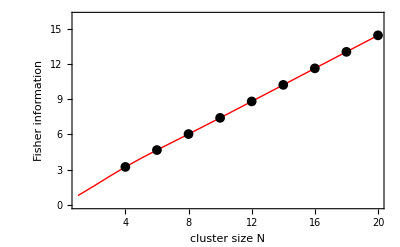

```mathematica
ColorData[97, "ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

#### Compare with Gaussian

```mathematica
gaussian[x_, mu_, sigma_]:= 1/(Sqrt[2 Pi]sigma) Exp[-(x-mu)^2/(2 sigma^2)]
Integrate[gaussian[x, 0, 1], {x, -Infinity, Infinity}]
```

1

```mathematica
tlist = Table[(2/10)*ti/200, {ti, 0, 200}];
pdflist = Table[{tlist[[i]], N[pdf[tlist[[i]], 10, 10,-2], 6]}, {i, 1, Length[tlist]}];
pdflist2 = Table[{tlist[[i]], N[pdf[tlist[[i]], 10, 10,-19/10], 6]}, {i, 1, Length[tlist]}];
```

N::meprec: Internal precision limit $MaxExtraPrecision = 200. reached while evaluating (3628800 (ⅇ^(375/1003)+ⅇ^(2506/1003)) (ⅇ^(1250/3009)+ⅇ^(23054/9027)) «6» (ⅇ^(1875/1003)+ⅇ^(4506/1003)) (ⅇ^(3750/1003)+ⅇ^(7006/1003)))/((ⅇ^(3750/1003)+ⅇ^(7006/1003)-2 (ⅇ^(1875/1003)+ⅇ^(4506/1003))) «7» (3 (ⅇ^(1250/1003)+ⅇ^(11018/3009))-2 (ⅇ^(1875/1003)+ⅇ^(4506/1003))))+(3628800 «10»)/((«1») «7» («1»))+«6»+(«1»)/(«1»)+(3628800 «9» (ⅇ^(«1»)+ⅇ^(«1»)))/(«1»).

N::meprec: Internal precision limit $MaxExtraPrecision = 200. reached while evaluating (3628800 (ⅇ^(375/1003)+ⅇ^(24057/10030)) (ⅇ^(1250/3009)+ⅇ^(221513/90270)) «6» (ⅇ^(1875/1003)+ⅇ^(44057/10030)) (ⅇ^(3750/1003)+ⅇ^(69057/10030)))/((ⅇ^(3750/1003)+ⅇ^(69057/10030)-2 (ⅇ^(1875/1003)+ⅇ^(44057/10030))) («1») «5» (4 («1»)-2 «1») (3 (ⅇ^(1250/1003)+ⅇ^(107171/30090))-2 (ⅇ^(1875/1003)+ⅇ^(44057/«4»0))))+(«1»)/(«1»)+«6»+(«1»)/(«1»)+(«1»)/(«1»).

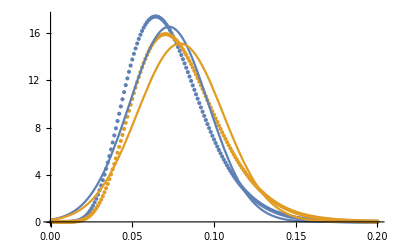

```mathematica
Show[
ListPlot[{pdflist, pdflist2}, PlotRange->All],
Plot[{gaussian[x, tmean[10, 10, -2], Sqrt[tvar[10, 10, -2]]],
gaussian[x, tmean[10, 10, -1.9], Sqrt[tvar[10, 10, -1.9]]]
}, {x, 0, 0.2}, PlotRange->All]
]
```

```mathematica
Series[1-Erf[(t0-al)/Sqrt[2]]+Erf[(t1-al)/Sqrt[2]]-Erf[(t0-al)/Sqrt[2]]Erf[(t1-al)/Sqrt[2]], {t1, t0, 1}]
```

(1-Erf[(-al+t0)/(√2)]^2)-ⅇ^(-1/2 (al-t0)^2) √(2/π) (-1+Erf[(-al+t0)/(√2)]) (t1-t0)+O[t1-t0]^2

```mathematica
Erf[0]
```

0

```mathematica
Expand[(1-x)^3/32+(1+x)/8 +(1-x)^2(1+x)/32 + (1-x^2)/8]
```

5/16-x^2/16

```mathematica
Simplify[%]
```

1/32 (11-x-3 x^2+x^3)

```mathematica
Together[11-x-3 x^2+x^3]
```

11-x-3 x^2+x^3